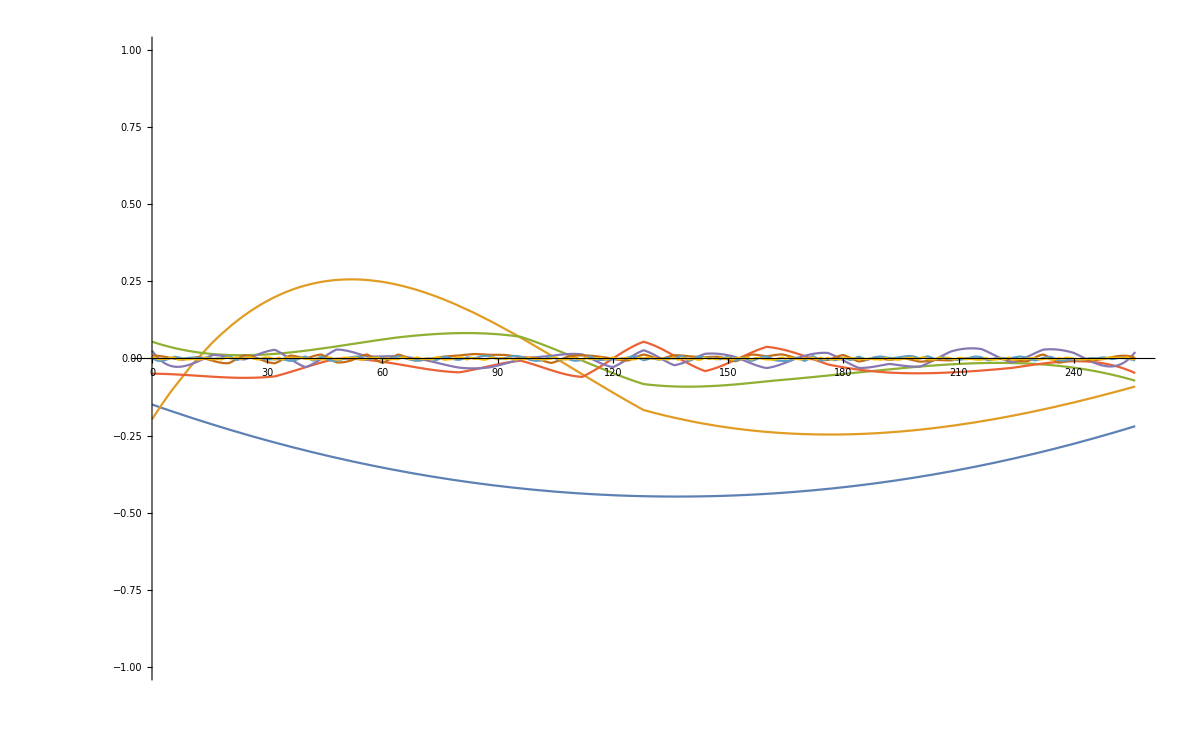

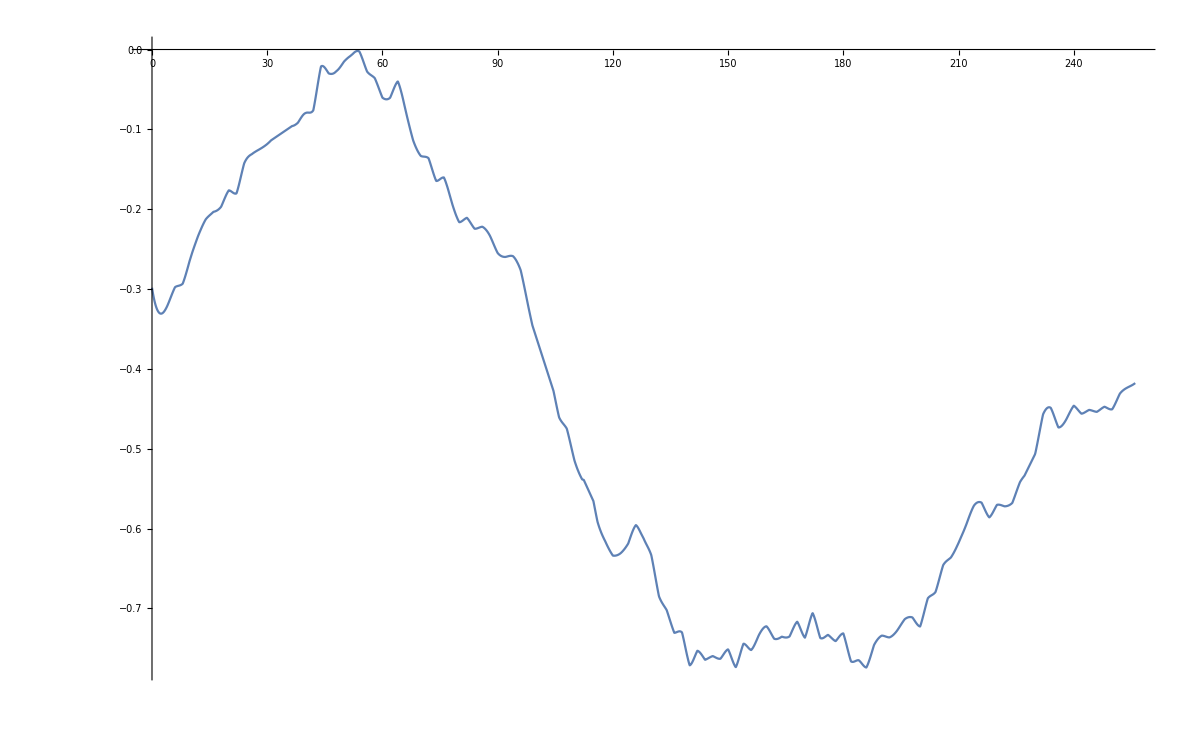

```mathematica
SeedRandom[27];
r0=Table[{i*2^8, RandomReal[{-1,1}]/2^0}, {i, 0, 2^0}];
r1=Table[{i*2^7, RandomReal[{-1,1}]/2^1}, {i, 0, 2^1}];
r2=Table[{i*2^6, RandomReal[{-1,1}]/2^2}, {i, 0, 2^2}];
r3=Table[{i*2^5, RandomReal[{-1,1}]/2^3}, {i, 0, 2^3}];
r4=Table[{i*2^4, RandomReal[{-1,1}]/2^4}, {i, 0, 2^4}];
r5=Table[{i*2^3, RandomReal[{-1,1}]/2^5}, {i, 0, 2^5}];
r6=Table[{i*2^2, RandomReal[{-1,1}]/2^6}, {i, 0, 2^6}];
r7=Table[{i*2^1, RandomReal[{-1,1}]/2^7}, {i, 0, 2^7}];
r8=Table[{i*2^0, RandomReal[{-1,1}]/2^8}, {i, 0, 2^8}];
i0 = Interpolation[r0, InterpolationOrder->1];
i1 = Interpolation[r1, InterpolationOrder->2];
i2 = Interpolation[r2, InterpolationOrder->3];
i3= Interpolation[r3, InterpolationOrder->3];
i4 = Interpolation[r4, InterpolationOrder->3];
i5 = Interpolation[r5, InterpolationOrder->3];
i6 = Interpolation[r6, InterpolationOrder->3];
i7 = Interpolation[r7, InterpolationOrder->3];
i8 = Interpolation[r8, InterpolationOrder->3];
Plot[{ i1[x], i2[x], i3[x], i4[x],i5[x], i6[x],i7[x], i8[x]}, {x, 0, 256}, PlotRange->{-1, 1}]
Plot[(i1[x]+i2[x]+i3[x]+i4[x]+i5[x]+i6[x]+i7[x]+i7[x]), {x, 0, 256}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

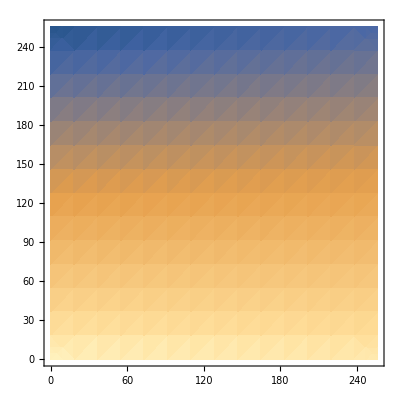
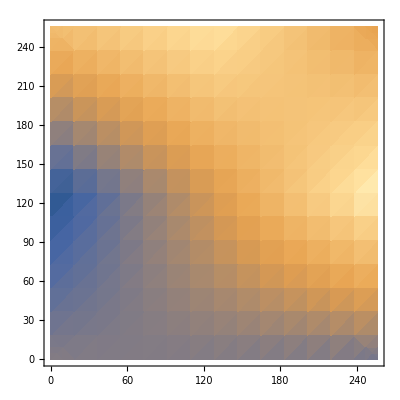
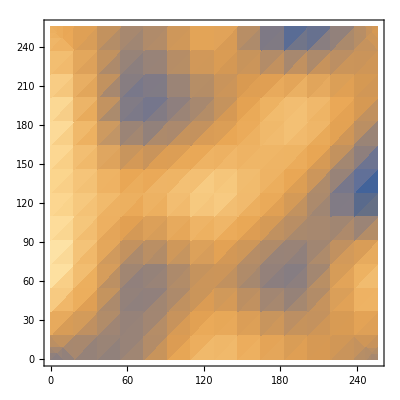
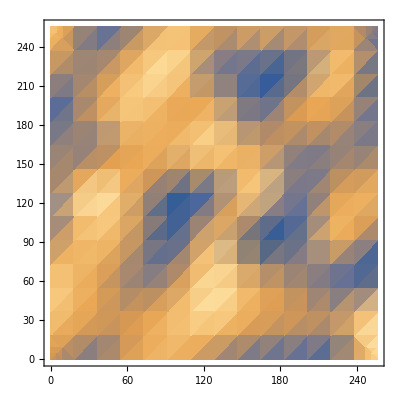
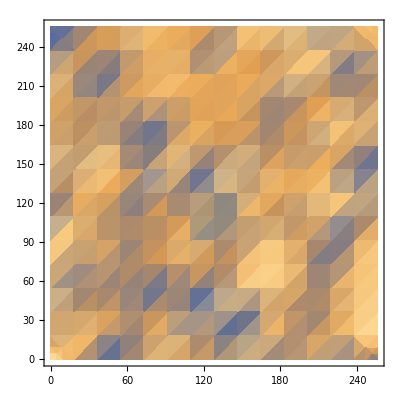
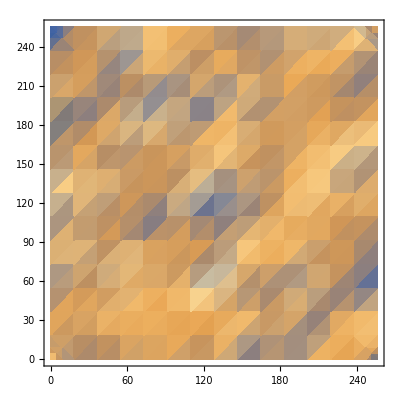
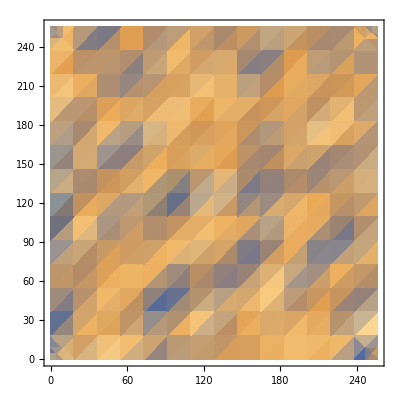
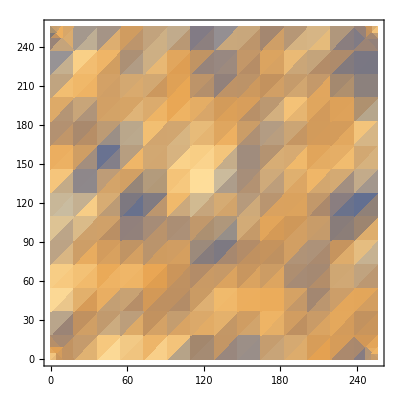

```mathematica
SeedRandom[1];
r0=Table[{{i*2^8,j*2^8}, RandomReal[{-1,1}]/2^0}, {i, 0, 2^0}, {j, 0, 2^0}];
r1=Table[{i*2^7,j*2^7, RandomReal[{-1,1}]/2^1}, {i, 0, 2^1}, {j, 0, 2^1}];
r2=Table[{i*2^6,j*2^6, RandomReal[{-1,1}]/2^2}, {i, 0, 2^2}, {j, 0, 2^2}];
r3=Table[{i*2^5,j*2^5, RandomReal[{-1,1}]/2^3}, {i, 0, 2^3}, {j, 0, 2^3}];
r4=Table[{i*2^4,j*2^4, RandomReal[{-1,1}]/2^4}, {i, 0, 2^4}, {j, 0, 2^4}];
r5=Table[{i*2^3,j*2^3, RandomReal[{-1,1}]/2^5}, {i, 0, 2^5}, {j, 0, 2^5}];
r6=Table[{i*2^2,j*2^2, RandomReal[{-1,1}]/2^6}, {i, 0, 2^6}, {j, 0, 2^6}];
r7=Table[{i*2^1,j*2^1, RandomReal[{-1,1}]/2^7}, {i, 0, 2^7}, {j, 0, 2^7}];
r8=Table[{i*2^0, j*2^0,RandomReal[{-1,1}]/2^8}, {i, 0, 2^8}, {j, 0, 2^8}];
i0 = Interpolation[Flatten[r0, 1], InterpolationOrder->{1,1}];
i1 = Interpolation[Flatten[r1, 1], InterpolationOrder->{1,1}];
i2 = Interpolation[Flatten[r2, 1], InterpolationOrder->{1, 1}];
i3= Interpolation[Flatten[r3, 1], InterpolationOrder->{1,1}];
i4 = Interpolation[Flatten[r4, 1], InterpolationOrder->{1,1}];
i5 = Interpolation[Flatten[r5, 1], InterpolationOrder->{1,1}];
i6 = Interpolation[Flatten[r6, 1], InterpolationOrder->{1,1}];
i7 = Interpolation[Flatten[r7, 1], InterpolationOrder->{1, 1}];
i8 = Interpolation[Flatten[r8, 1], InterpolationOrder->{1, 1}];
List[Plot3D[i0[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i1[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i2[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i3[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i4[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i5[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i6[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i7[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
Plot3D[i8[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}]]
Plot3D[i1[x,y]+i2[x,y]+i3[x,y]+i4[x,y]+i5[x,y]+i6[x,y]+i7[x,y]+i7[x,y], {x, 0, 256}, {y, 0, 256}]
List[DensityPlot[i0[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i1[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i2[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i3[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i4[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i5[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i6[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i7[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}],
DensityPlot[i8[x,y], {x, 0, 256},{y, 0, 256}, PlotRange->{-1, 1}]]
DensityPlot[i1[x,y]+i2[x,y]+i3[x,y]+i4[x,y]+i5[x,y]+i6[x,y]+i7[x,y]+i8[x,y], {x, 0, 256}, {y, 0, 256}, PlotPoints->50]
```

```mathematica
DensityPlot[FractionalPart[(Cos[x/20]/2+i2[x,y]+i3[x,y])*20], {x, 50, 150}, {y,50, 150},ColorFunction->"RustTones", PlotPoints->100]
```

-Graphics-